```mathematica
levelNames ={"a1","a2","b1","b2"};
```

```mathematica
rootPath = NotebookDirectory[];
```

```mathematica
texts = Table[Import[ FileNameJoin[{rootPath , "data","sentences" ,StringJoin[ level," sentences.txt"]}]],{level,levelNames}];
```

```mathematica
TextSentences[texts[[1]],4] (*Show 4 sentences, only A1 level*)
```

{I would like that, my dear.,I would like to order  la carte.,I would like to compose a message.,Beautiful work.}

```mathematica
Flatten[TextSentences[#,1]&@texts](*Show 1 sentence, all levels in one array*)
```

{I would like that, my dear.,That’s Speedy!,And guess what?,He couldn't even guess.}

```mathematica
sentencesFull=TextSentences[#]&@texts;
```

```mathematica
nSents =All;
```

```mathematica
sentences= Map[Take[#,nSents]&,sentencesFull];
```

```mathematica
nameLength={levelNames,Map[Length,sentences]}ᵀ;
```

```mathematica
(*sent2d = DimensionReduce[Flatten[sentences],2];*)
```

```mathematica
labels=Flatten[Table[Table[x[[1]],x[[2]]],{x,nameLength}]];
```

```mathematica
(*byLevels=GroupBy[Thread[sent2d->labels],Last->First];*)
```

```mathematica
(*ListPlot[Values[byLevels],PlotLegends->Keys[byLevels],PlotStyle->PointSize[Medium]]*)
```

```mathematica
allData=Thread[Flatten[sentences]->labels];
```

```mathematica
trainingData = RandomSample[allData,Round[0.7Length[allData]]];
```

```mathematica
testingData=Complement[allData,trainingData];
```

```mathematica
trainedClassifier=Classify[trainingData]
```

ClassifierFunction[…]

```mathematica
cm=ClassifierMeasurements[trainedClassifier,testingData]
ClassifierMeasurementsObject[…]
```

ClassifierMeasurementsObject[…]

General::noinfo: Input expression ClassifierMeasurementsObject[…] contains insufficient information to interpret the result.

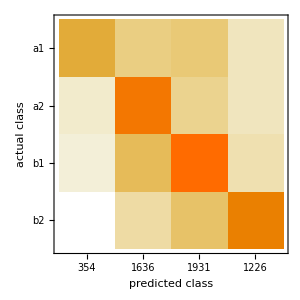

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
cm["Accuracy"]
```

0.822227